# Mathematica Homework 4

Brian Carlson and Sam Booth 2-28-2014

## Problem 1. Dice-game

### Task

(i) Assume that you are rolling two dice at the same time and add the two numbers you get - that means you can get numbers from 2 to 12. Compute the probabilities for each outcome and report the results in the table below. 

(ii) Write a function uDicegame[utaPick,clausPick] with two parameters: the number utaPick picked by Uta and the number clausPick picked by Claus. The function uDicegame[utaPick,clausPick] returns a list that contains three elements {lastUta,lastClaus,rolls} where lastUta and lastClaus are the results of the last roll of the dice, that is the first roll of the dice where either Uta rolled utaPick or Claus rolled clausPick (or both). rolls is the number of rolls it took to get there.

(iii) Write a function countingWinner[session,utaPick,clausPick] which simulates session games where Uta always picks utaPick and Claus always picks clausPick. The function returns a list of three elements {(wins for Uta)/(games played),(wins for Claus)/(games played),(total number or rolls)/(games played)}. For very large values of session the first two entries are estimates for the probabilities. The first entry gives the approximate probability that Uta wins if Uta picks utaPick and Claus picks clausPick. The second entry gives the approximate probability that Claus wins if Uta picks utaPick and Claus picks clausPick.

(iv) Run countingWinner[session,utaPick,clausPick] for session equal one million (that is m=10^6) for all possible combinations of choices utaPick and clausPick.
Collect all the results in a list called resultsonemilliongames.
An element of resultsonemilliongames should have the following form
{utaPick,clausPick,(wins for Uta)/(games played),(wins for Claus)/(games played),(total number or rolls)/(games played)}

(v) Use TableForm to create a table of probabilities that Uta wins by extracting these probabilities from your list resultsonemilliongames.

(vi) Use TableForm to create a table of the length of the game by extracting the number of rolls from your list resultsonemilliongames.

(vii) Try to make observations about the probability values you observed in part (v) and (vi). Remember that the numbers are the results of random experiments, so they are approximations of the real values. Moreover if you rerun the computations you will get slightly different answers.

### Solution (i)

```mathematica
(* This code uses the uniform distribution function to determine the probability of any sum occuring where each dice has the values 1 though 6.*)
Grid[{Range[2,12],Table[Probability[Dice1 + Dice2 == sum, {Dice1 \[Distributed] DiscreteUniformDistribution[{1,6}],Dice2 \[Distributed] DiscreteUniformDistribution[{1,6}]}],{sum,2,12}]},Frame->All,Spacings -> 2]

{{2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {1/36, 1/18, 1/12, 1/9, 5/36, 1/6, 5/36, 1/9, 1/12, 1/18, 1/36}}
```

### Solution (ii)

```mathematica
(* This function takes in a dice sum value for uta and a dice sum value for claus, it then generates a sum of two random integers of values 1 through 6. If uta's pick matches, she wins, if claus's pick wins where uta's didn't,he wins, otherwise the process repeats *)
```

```mathematica
uDiceGame[utaPick_,clausPick_] := Module[{utaCurrent = RandomInteger[{1,6}]+RandomInteger[{1,6}],clausCurrent = RandomInteger[{1,6}] RandomInteger[{1,6}],count = 1},
diceList = {utaCurrent,clausCurrent};
While[(utaCurrent ≠ utaPick )&& (clausCurrent ≠ clausPick), 
utaCurrent = RandomInteger[{1,6}]+RandomInteger[{1,6}];
clausCurrent = RandomInteger[{1,6}]+RandomInteger[{1,6}];
count ++;
];
(*The values of the initial picks are released as well as the number of turns it took for a winner to be reached *)
Return[diceList = {utaCurrent,clausCurrent,count}];
]
```

#### Test Cases (ii)

```mathematica
uDiceGame[7,7]
```

{7,11,3}

```mathematica
uDiceGame[2,12]
```

{2,11,27}

```mathematica
uDiceGame[4,4]
```

{4,4,9}

### Solution (iii)

```mathematica
(*  This function takes dice sum value for uta and a dice sum value for claus, and a session value for a number of repetitions. Where every repetition the gamestats are set to the results of the uDiceGame and the winner is calculated. Each winner adds one to their total count for final results. The number of turns for each game is also stored for calculations at the end *)
```

```mathematica
countingWinner[session_,utaPick_,clausPick_] := Module[{count = 1,utaCounter = 0,clausCounter= 0,gameStats = uDiceGame[utaPick,clausPick],totalCount},totalCount = gameStats[[3]]; 
While[count ≤ session, 
If[gameStats[[1]]  == utaPick,utaCounter++,clausCounter++];
totalCount += gameStats[[3]];
gameStats = uDiceGame[utaPick,clausPick];
count++
];
Return[{N[utaCounter/session],N[clausCounter/session],N[totalCount/session]}]
]
```

#### Test Cases (iii)

```mathematica
countingWinner[8,7,5]
```

{0.875,0.125,4.}

```mathematica
countingWinner[20,2,12]
```

{0.55,0.45,19.6}

```mathematica
countingWinner[10,5,11]
```

{0.7,0.3,5.8}

### Solution (iv)

```mathematica
(* Runs coutningWinner for one million sessions on every combination of uta picks and clause picks and prepends the current picks to each element of the final list.
"ParallelTable" cuts down on the computing time required. *)
```

```mathematica
resultsonemilliongames =ParallelTable[Flatten[Prepend[countingWinner[1000000,j,k],{j,k}]],{j,2,12},{k,2,12}]
```

{{{2,2,0.49376,0.50624,17.7249},{2,3,0.339523,0.660477,12.2218},{2,4,0.255648,0.744352,9.18967},{2,5,0.216036,0.783964,7.74885},{2,6,0.175583,0.824417,6.30371},{2,7,0.170442,0.829558,6.12419},{2,8,0.183984,0.816016,6.6372},{2,9,0.2209,0.7791,7.96851},{2,10,0.261797,0.738203,9.45009},{2,11,0.358114,0.641886,12.8963},{2,12,0.465422,0.534578,16.7661}},{{3,2,0.660823,0.339177,11.8997},{3,3,0.514635,0.485365,9.2556},{3,4,0.412818,0.587182,7.43887},{3,5,0.364186,0.635814,6.55852},{3,6,0.30481,0.69519,5.49352},{3,7,0.301365,0.698635,5.43301},{3,8,0.321571,0.678429,5.77621},{3,9,0.37322,0.62678,6.71022},{3,10,0.424282,0.575718,7.64821},{3,11,0.540648,0.459352,9.73519},{3,12,0.626408,0.373592,11.2863}},{{4,2,0.746686,0.253314,8.96183},{4,3,0.620004,0.379996,7.43849},{4,4,0.521585,0.478415,6.26567},{4,5,0.474021,0.525979,5.67029},{4,6,0.404907,0.595093,4.86355},{4,7,0.407293,0.592707,4.87893},{4,8,0.425882,0.574118,5.10553},{4,9,0.484761,0.515239,5.81585},{4,10,0.534658,0.465342,6.42766},{4,11,0.652519,0.347481,7.82706},{4,12,0.706896,0.293104,8.49116}},{{5,2,0.797389,0.202611,7.19329},{5,3,0.692677,0.307323,6.22975},{5,4,0.600158,0.399842,5.39939},{5,5,0.555577,0.444423,5.01084},{5,6,0.485111,0.514889,4.36362},{5,7,0.493242,0.506758,4.43229},{5,8,0.508875,0.491125,4.58242},{5,9,0.569072,0.430928,5.12272},{5,10,0.614606,0.385394,5.53566},{5,11,0.726199,0.273801,6.53308},{5,12,0.757092,0.242908,6.81171}},{{6,2,0.832757,0.167243,5.98117},{6,3,0.744152,0.255848,5.35808},{6,4,0.659017,0.340983,4.75692},{6,5,0.620395,0.379605,4.46957},{6,6,0.550137,0.449863,3.96554},{6,7,0.562688,0.437312,4.04948},{6,8,0.575506,0.424494,4.1459},{6,9,0.635004,0.364996,4.57261},{6,10,0.675155,0.324845,4.85864},{6,11,0.779685,0.220315,5.60467},{6,12,0.791724,0.208276,5.70123}},{{7,2,0.857414,0.142586,5.14184},{7,3,0.782443,0.217557,4.69747},{7,4,0.705884,0.294116,4.23738},{7,5,0.67291,0.32709,4.03908},{7,6,0.605353,0.394647,3.626},{7,7,0.621704,0.378296,3.72893},{7,8,0.631003,0.368997,3.78972},{7,9,0.687585,0.312415,4.1269},{7,10,0.721637,0.278363,4.33146},{7,11,0.819408,0.180592,4.90666},{7,12,0.817548,0.182452,4.90084}},{{8,2,0.832463,0.167537,5.9939},{8,3,0.744139,0.255861,5.35513},{8,4,0.659466,0.340534,4.7465},{8,5,0.619416,0.380584,4.46826},{8,6,0.550038,0.449962,3.96139},{8,7,0.563578,0.436422,4.04391},{8,8,0.575867,0.424133,4.14658},{8,9,0.634147,0.365853,4.56845},{8,10,0.675158,0.324842,4.85911},{8,11,0.779752,0.220248,5.60812},{8,12,0.791356,0.208644,5.68795}},{{9,2,0.797254,0.202746,7.17622},{9,3,0.692025,0.307975,6.22523},{9,4,0.600905,0.399095,5.40061},{9,5,0.555341,0.444659,4.99459},{9,6,0.485413,0.514587,4.37267},{9,7,0.492754,0.507246,4.42452},{9,8,0.508169,0.491831,4.58488},{9,9,0.569013,0.430987,5.12317},{9,10,0.614747,0.385253,5.53772},{9,11,0.726651,0.273349,6.52983},{9,12,0.757639,0.242361,6.81706}},{{10,2,0.746542,0.253458,8.96611},{10,3,0.619741,0.380259,7.44824},{10,4,0.522443,0.477557,6.26062},{10,5,0.473239,0.526761,5.67298},{10,6,0.405561,0.594439,4.86471},{10,7,0.407589,0.592411,4.88364},{10,8,0.426309,0.573691,5.10132},{10,9,0.484123,0.515877,5.81154},{10,10,0.535096,0.464904,6.41552},{10,11,0.653405,0.346595,7.82695},{10,12,0.707125,0.292875,8.48589}},{{11,2,0.661772,0.338228,11.9015},{11,3,0.514656,0.485344,9.25763},{11,4,0.413865,0.586135,7.45455},{11,5,0.364748,0.635252,6.55465},{11,6,0.305599,0.694401,5.49355},{11,7,0.301827,0.698173,5.43324},{11,8,0.320822,0.679178,5.77985},{11,9,0.373317,0.626683,6.72987},{11,10,0.425699,0.574301,7.657},{11,11,0.541187,0.458813,9.74128},{11,12,0.626008,0.373992,11.2703}},{{12,2,0.494015,0.505985,17.7723},{12,3,0.339701,0.660299,12.2304},{12,4,0.254898,0.745102,9.20393},{12,5,0.215356,0.784644,7.76487},{12,6,0.176011,0.823989,6.30906},{12,7,0.170269,0.829731,6.12142},{12,8,0.183938,0.816062,6.64335},{12,9,0.221057,0.778943,7.95683},{12,10,0.261794,0.738206,9.45618},{12,11,0.358686,0.641314,12.91},{12,12,0.465909,0.534091,16.8127}}}

```mathematica
Grid[resultsonemilliongames, Frame -> All,Alignment -> Right]
{{{2,2,0.49376,0.50624,17.724918}, {2,3,0.339523,0.660477,12.22178}, {2,4,0.255648,0.744352,9.18967}, {2,5,0.216036,0.783964,7.748852}, {2,6,0.175583,0.824417,6.303712}, {2,7,0.170442,0.829558,6.124188}, {2,8,0.183984,0.816016,6.637196}, {2,9,0.2209,0.7791,7.96851}, {2,10,0.261797,0.738203,9.450085}, {2,11,0.358114,0.641886,12.896315}, {2,12,0.465422,0.534578,16.766062}}, {{3,2,0.660823,0.339177,11.899669}, {3,3,0.514635,0.485365,9.255603}, {3,4,0.412818,0.587182,7.438871}, {3,5,0.364186,0.635814,6.558519}, {3,6,0.30481,0.69519,5.493516}, {3,7,0.301365,0.698635,5.433005}, {3,8,0.321571,0.678429,5.776205}, {3,9,0.37322,0.62678,6.710219}, {3,10,0.424282,0.575718,7.648206}, {3,11,0.540648,0.459352,9.735192}, {3,12,0.626408,0.373592,11.286306}}, {{4,2,0.746686,0.253314,8.961833}, {4,3,0.620004,0.379996,7.438485}, {4,4,0.521585,0.478415,6.265669}, {4,5,0.474021,0.525979,5.670293}, {4,6,0.404907,0.595093,4.863553}, {4,7,0.407293,0.592707,4.878933}, {4,8,0.425882,0.574118,5.105525}, {4,9,0.484761,0.515239,5.815849}, {4,10,0.534658,0.465342,6.427662}, {4,11,0.652519,0.347481,7.82706}, {4,12,0.706896,0.293104,8.491163}}, {{5,2,0.797389,0.202611,7.193292}, {5,3,0.692677,0.307323,6.229752}, {5,4,0.600158,0.399842,5.399391}, {5,5,0.555577,0.444423,5.010836}, {5,6,0.485111,0.514889,4.363623}, {5,7,0.493242,0.506758,4.432287}, {5,8,0.508875,0.491125,4.582424}, {5,9,0.569072,0.430928,5.122719}, {5,10,0.614606,0.385394,5.535661}, {5,11,0.726199,0.273801,6.53308}, {5,12,0.757092,0.242908,6.811712}}, {{6,2,0.832757,0.167243,5.981172}, {6,3,0.744152,0.255848,5.358076}, {6,4,0.659017,0.340983,4.756915}, {6,5,0.620395,0.379605,4.469572}, {6,6,0.550137,0.449863,3.965539}, {6,7,0.562688,0.437312,4.049478}, {6,8,0.575506,0.424494,4.145899}, {6,9,0.635004,0.364996,4.572609}, {6,10,0.675155,0.324845,4.85864}, {6,11,0.779685,0.220315,5.604667}, {6,12,0.791724,0.208276,5.701228}}, {{7,2,0.857414,0.142586,5.141835}, {7,3,0.782443,0.217557,4.697467}, {7,4,0.705884,0.294116,4.237381}, {7,5,0.67291,0.32709,4.039081}, {7,6,0.605353,0.394647,3.625998}, {7,7,0.621704,0.378296,3.728932}, {7,8,0.631003,0.368997,3.789715}, {7,9,0.687585,0.312415,4.126899}, {7,10,0.721637,0.278363,4.331464}, {7,11,0.819408,0.180592,4.906661}, {7,12,0.817548,0.182452,4.900835}}, {{8,2,0.832463,0.167537,5.993903}, {8,3,0.744139,0.255861,5.355126}, {8,4,0.659466,0.340534,4.746499}, {8,5,0.619416,0.380584,4.468263}, {8,6,0.550038,0.449962,3.961385}, {8,7,0.563578,0.436422,4.043907}, {8,8,0.575867,0.424133,4.146581}, {8,9,0.634147,0.365853,4.568448}, {8,10,0.675158,0.324842,4.859107}, {8,11,0.779752,0.220248,5.608124}, {8,12,0.791356,0.208644,5.68795}}, {{9,2,0.797254,0.202746,7.176223}, {9,3,0.692025,0.307975,6.22523}, {9,4,0.600905,0.399095,5.400608}, {9,5,0.555341,0.444659,4.994591}, {9,6,0.485413,0.514587,4.372673}, {9,7,0.492754,0.507246,4.424524}, {9,8,0.508169,0.491831,4.584882}, {9,9,0.569013,0.430987,5.123165}, {9,10,0.614747,0.385253,5.537719}, {9,11,0.726651,0.273349,6.52983}, {9,12,0.757639,0.242361,6.817059}}, {{10,2,0.746542,0.253458,8.966106}, {10,3,0.619741,0.380259,7.448244}, {10,4,0.522443,0.477557,6.260616}, {10,5,0.473239,0.526761,5.672978}, {10,6,0.405561,0.594439,4.864712}, {10,7,0.407589,0.592411,4.883641}, {10,8,0.426309,0.573691,5.101323}, {10,9,0.484123,0.515877,5.811538}, {10,10,0.535096,0.464904,6.415524}, {10,11,0.653405,0.346595,7.826948}, {10,12,0.707125,0.292875,8.485889}}, {{11,2,0.661772,0.338228,11.901471}, {11,3,0.514656,0.485344,9.257628}, {11,4,0.413865,0.586135,7.454551}, {11,5,0.364748,0.635252,6.554652}, {11,6,0.305599,0.694401,5.493547}, {11,7,0.301827,0.698173,5.433238}, {11,8,0.320822,0.679178,5.779847}, {11,9,0.373317,0.626683,6.729874}, {11,10,0.425699,0.574301,7.657}, {11,11,0.541187,0.458813,9.741275}, {11,12,0.626008,0.373992,11.27026}}, {{12,2,0.494015,0.505985,17.772306}, {12,3,0.339701,0.660299,12.230433}, {12,4,0.254898,0.745102,9.203927}, {12,5,0.215356,0.784644,7.764865}, {12,6,0.176011,0.823989,6.309062}, {12,7,0.170269,0.829731,6.121417}, {12,8,0.183938,0.816062,6.643348}, {12,9,0.221057,0.778943,7.956828}, {12,10,0.261794,0.738206,9.456177}, {12,11,0.358686,0.641314,12.910018}, {12,12,0.465909,0.534091,16.812693}}}
```

### Solution (v)

```mathematica
(* Table form of every uta win in all sum choice combinations *)
```

```mathematica
TableForm[Table[Take[Flatten[Take[resultsonemilliongames,All,All,{3}]],{(10j+1)+j,(10j+11)+j}],{j,0,10}], TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 0.49376 | 0.339523 | 0.255648 | 0.216036 | 0.175583 | 0.170442 | 0.183984 | 0.2209 | 0.261797 | 0.358114 | 0.465422
3 | 0.660823 | 0.514635 | 0.412818 | 0.364186 | 0.30481 | 0.301365 | 0.321571 | 0.37322 | 0.424282 | 0.540648 | 0.626408
4 | 0.746686 | 0.620004 | 0.521585 | 0.474021 | 0.404907 | 0.407293 | 0.425882 | 0.484761 | 0.534658 | 0.652519 | 0.706896
5 | 0.797389 | 0.692677 | 0.600158 | 0.555577 | 0.485111 | 0.493242 | 0.508875 | 0.569072 | 0.614606 | 0.726199 | 0.757092
6 | 0.832757 | 0.744152 | 0.659017 | 0.620395 | 0.550137 | 0.562688 | 0.575506 | 0.635004 | 0.675155 | 0.779685 | 0.791724
7 | 0.857414 | 0.782443 | 0.705884 | 0.67291 | 0.605353 | 0.621704 | 0.631003 | 0.687585 | 0.721637 | 0.819408 | 0.817548
8 | 0.832463 | 0.744139 | 0.659466 | 0.619416 | 0.550038 | 0.563578 | 0.575867 | 0.634147 | 0.675158 | 0.779752 | 0.791356
9 | 0.797254 | 0.692025 | 0.600905 | 0.555341 | 0.485413 | 0.492754 | 0.508169 | 0.569013 | 0.614747 | 0.726651 | 0.757639
10 | 0.746542 | 0.619741 | 0.522443 | 0.473239 | 0.405561 | 0.407589 | 0.426309 | 0.484123 | 0.535096 | 0.653405 | 0.707125
11 | 0.661772 | 0.514656 | 0.413865 | 0.364748 | 0.305599 | 0.301827 | 0.320822 | 0.373317 | 0.425699 | 0.541187 | 0.626008
12 | 0.494015 | 0.339701 | 0.254898 | 0.215356 | 0.176011 | 0.170269 | 0.183938 | 0.221057 | 0.261794 | 0.358686 | 0.465909

### Solution (vi)

```mathematica
(* Table form of every average run number in all sum choice combinations *)
```

```mathematica
TableForm[Table[Take[Flatten[Take[resultsonemilliongames,All,All,{-1}]],{(10j+1)+j,(10j+11)+j}],{j,0,10}], TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 17.7249 | 12.2218 | 9.18967 | 7.74885 | 6.30371 | 6.12419 | 6.6372 | 7.96851 | 9.45009 | 12.8963 | 16.7661
3 | 11.8997 | 9.2556 | 7.43887 | 6.55852 | 5.49352 | 5.43301 | 5.77621 | 6.71022 | 7.64821 | 9.73519 | 11.2863
4 | 8.96183 | 7.43849 | 6.26567 | 5.67029 | 4.86355 | 4.87893 | 5.10553 | 5.81585 | 6.42766 | 7.82706 | 8.49116
5 | 7.19329 | 6.22975 | 5.39939 | 5.01084 | 4.36362 | 4.43229 | 4.58242 | 5.12272 | 5.53566 | 6.53308 | 6.81171
6 | 5.98117 | 5.35808 | 4.75692 | 4.46957 | 3.96554 | 4.04948 | 4.1459 | 4.57261 | 4.85864 | 5.60467 | 5.70123
7 | 5.14184 | 4.69747 | 4.23738 | 4.03908 | 3.626 | 3.72893 | 3.78972 | 4.1269 | 4.33146 | 4.90666 | 4.90084
8 | 5.9939 | 5.35513 | 4.7465 | 4.46826 | 3.96139 | 4.04391 | 4.14658 | 4.56845 | 4.85911 | 5.60812 | 5.68795
9 | 7.17622 | 6.22523 | 5.40061 | 4.99459 | 4.37267 | 4.42452 | 4.58488 | 5.12317 | 5.53772 | 6.52983 | 6.81706
10 | 8.96611 | 7.44824 | 6.26062 | 5.67298 | 4.86471 | 4.88364 | 5.10132 | 5.81154 | 6.41552 | 7.82695 | 8.48589
11 | 11.9015 | 9.25763 | 7.45455 | 6.55465 | 5.49355 | 5.43324 | 5.77985 | 6.72987 | 7.657 | 9.74128 | 11.2703
12 | 17.7723 | 12.2304 | 9.20393 | 7.76487 | 6.30906 | 6.12142 | 6.64335 | 7.95683 | 9.45618 | 12.91 | 16.8127

### Solution (vii)

```mathematica
(* List for use in verification of conjectures *)
```

```mathematica
probList = Table[Probability[Dice1 + Dice2 == sum, {Dice1 \[Distributed] DiscreteUniformDistribution[{1,6}],Dice2 \[Distributed] DiscreteUniformDistribution[{1,6}]}],{sum,2,12}]
```

{1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36}

### Conjecture 1

The ratio of uta wins to  one claus win can be represented by the ratio ((probability that uta wins)/(probability that claus wins)). This ratio when over the same ratio plus one gives the total odds that uta should win any one game. However, if there is any tie uta will have won,so we must add to the final percentage the situation where uta ties with claus. This can be given by the equation  (chance uta wins) * (chance claus wins)
total probability of uta winning =( ((probability uta wins)/(probability claus wins))/(((probability uta wins)/(probability claus wins))+1)+(chance uta wins)*(chance claus wins))or utaWin% = (utaWinProbability)/(utaWinProbability+clausWinProbability)+(utaWinProbability)(clausWinProbability)

```mathematica
TableForm[Table[N[probList[[j-1]]/(probList[[j-1]]+probList[[k-1]])+probList[[j-1]]probList[[k-1]]],{j,2,12},{k,2,12}],TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 0.500772 | 0.334877 | 0.252315 | 0.203086 | 0.170525 | 0.147487 | 0.170525 | 0.203086 | 0.252315 | 0.334877 | 0.500772
3 | 0.66821 | 0.503086 | 0.40463 | 0.339506 | 0.29343 | 0.259259 | 0.29343 | 0.339506 | 0.40463 | 0.503086 | 0.66821
4 | 0.752315 | 0.60463 | 0.506944 | 0.437831 | 0.386574 | 0.347222 | 0.386574 | 0.437831 | 0.506944 | 0.60463 | 0.752315
5 | 0.803086 | 0.67284 | 0.580688 | 0.512346 | 0.459877 | 0.418519 | 0.459877 | 0.512346 | 0.580688 | 0.67284 | 0.803086
6 | 0.837191 | 0.722002 | 0.636574 | 0.570988 | 0.51929 | 0.477694 | 0.51929 | 0.570988 | 0.636574 | 0.722002 | 0.837191
7 | 0.861772 | 0.759259 | 0.680556 | 0.618519 | 0.568603 | 0.527778 | 0.568603 | 0.618519 | 0.680556 | 0.759259 | 0.861772
8 | 0.837191 | 0.722002 | 0.636574 | 0.570988 | 0.51929 | 0.477694 | 0.51929 | 0.570988 | 0.636574 | 0.722002 | 0.837191
9 | 0.803086 | 0.67284 | 0.580688 | 0.512346 | 0.459877 | 0.418519 | 0.459877 | 0.512346 | 0.580688 | 0.67284 | 0.803086
10 | 0.752315 | 0.60463 | 0.506944 | 0.437831 | 0.386574 | 0.347222 | 0.386574 | 0.437831 | 0.506944 | 0.60463 | 0.752315
11 | 0.66821 | 0.503086 | 0.40463 | 0.339506 | 0.29343 | 0.259259 | 0.29343 | 0.339506 | 0.40463 | 0.503086 | 0.66821
12 | 0.500772 | 0.334877 | 0.252315 | 0.203086 | 0.170525 | 0.147487 | 0.170525 | 0.203086 | 0.252315 | 0.334877 | 0.500772

### Conjecture 2

The odds that either of the sums are rolled are given by (odds of uta rolling the sum) + (odds of claus rolling the sum). Since the sum will either be acheived or not acheived on each trial it either passes or fails. The odds of a sum passing or failing is not affected by past outcomes. These facts show that the results will follow a geometric distribution, and therefore the average number of trials that are needed are given  by (1/odds that the sums are rolled).
average number of trials needed for a win = 1/(utaWinProbability+clausWinProbability)

```mathematica
TableForm[Table[N[1/(probList[[j-1]]+probList[[k-1]])],{j,2,12},{k,2,12}],TableHeadings -> {Range[2, 12], Range[2, 12]}]
```

| 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 18. | 12. | 9. | 7.2 | 6. | 5.14286 | 6. | 7.2 | 9. | 12. | 18.
3 | 12. | 9. | 7.2 | 6. | 5.14286 | 4.5 | 5.14286 | 6. | 7.2 | 9. | 12.
4 | 9. | 7.2 | 6. | 5.14286 | 4.5 | 4. | 4.5 | 5.14286 | 6. | 7.2 | 9.
5 | 7.2 | 6. | 5.14286 | 4.5 | 4. | 3.6 | 4. | 4.5 | 5.14286 | 6. | 7.2
6 | 6. | 5.14286 | 4.5 | 4. | 3.6 | 3.27273 | 3.6 | 4. | 4.5 | 5.14286 | 6.
7 | 5.14286 | 4.5 | 4. | 3.6 | 3.27273 | 3. | 3.27273 | 3.6 | 4. | 4.5 | 5.14286
8 | 6. | 5.14286 | 4.5 | 4. | 3.6 | 3.27273 | 3.6 | 4. | 4.5 | 5.14286 | 6.
9 | 7.2 | 6. | 5.14286 | 4.5 | 4. | 3.6 | 4. | 4.5 | 5.14286 | 6. | 7.2
10 | 9. | 7.2 | 6. | 5.14286 | 4.5 | 4. | 4.5 | 5.14286 | 6. | 7.2 | 9.
11 | 12. | 9. | 7.2 | 6. | 5.14286 | 4.5 | 5.14286 | 6. | 7.2 | 9. | 12.
12 | 18. | 12. | 9. | 7.2 | 6. | 5.14286 | 6. | 7.2 | 9. | 12. | 18.

## Problem 2. Five Nested Circles

### Task

(i) Write a function uFiveCircles[radius1, radius2, radius3] which is given 3 radii (positive values) and which computes and returns the information about an arrangement of 5 circles. Each element in the list describes a circle using three values {{xcenter,ycenter},rad} where {xcenter,ycenter} is the center of the circle and rad is the radius.

(ii) Using the work of part (i) write a function uDisplayFiveCircles[radius1, radius2, radius3] 
that creates a graphic of the five circles with three circles of the given radii in black and the other two circles in two different colors of your choice (which are not black).

### Solution (i)

```mathematica
(*This function computes the x-coordinates, y-coordinates, and radii of 5 circles, given the radius of 3 of them, with the assumption that the first two sit on the x-axis*)
```

```mathematica
uFiveCircles[radius1_,radius2_,radius3_]:= Module[{x1,y1,x2,y2,x3,y3,x4,x5,y4,y5,radius4,radius5,solution={},i},
(*First, we solve for the x and y values of the two circles sitting on the x-axis using the program we wrote in class*)
{{x1,y1},{x2,y2}}=findTwoCenters[radius1,radius2];
(*Next, we find the x and y values for the third circle, tangent to both the first and second*)
{x3,y3}={x3,y3}/.NSolve[{(radius2+radius3)^2==(x2-x3)^2+(y2-y3)^2,(radius1+radius3)^2==(x3-x1)^2+(y3-y1)^2},{x3,y3}][[2]];
(*When we find the x and y values for the fourth circle, we must also solve for the radius*)
{x4,y4,radius4}={x4,y4,radius4}/.NSolve[{
(radius4+radius3)^2==(x4-x3)^2+(y4-y3)^2,
(radius1+radius4)^2==(x4-x1)^2+(y4-y1)^2,
(radius4+radius2)^2==(x4-x2)^2+(y4-y2)^2
},
{x4,y4,radius4}][[2]];
(*Sometimes, "NSolve" will give a negative radius from the entered systems of equations, if this is the case, we should check the other value that "NSolve" provided us*)
If[radius4<0,
{x4,y4,radius4}={x4,y4,radius4}/.NSolve[{
(radius4+radius3)^2==(x4-x3)^2+(y4-y3)^2,
(radius1+radius4)^2==(x4-x1)^2+(y4-y1)^2,
(radius4+radius2)^2==(x4-x2)^2+(y4-y2)^2
},
{x4,y4,radius4}][[1]];
];
(*This "NSolve" accounts for if the fifth circle is surrounding the first three circles*)
solution=NSolve[{
(radius5-radius1)^2==(x5-x1)^2+(y5-y1)^2,
(radius5-radius2)^2==(x5-x2)^2+(y5-y2)^2,
(radius5-radius3)^2==(x5-x3)^2+(y5-y3)^2
},
{x5,y5,radius5}
];

{x5,y5,radius5}={x5,y5,radius5}/.(solution[[2]]);
If[radius5<0,
{x5,y5,radius5}={x5,y5,radius5}/.(solution[[1]]);
];
(*This "NSolve" accounts for if the fifth circle isn't surrounding the first three circles*)
If[solution=={},
solution=NSolve[{
(radius1+radius5)^2==(x5-x1)^2+(y5-y1)^2,
(radius5+radius2)^2==(x5-x2)^2+(y5-y2)^2,
(radius5+radius3)^2==(x5-x3)^2+(y5-y3)^2
},
{x5,y5,radius5}
];
If[solution≠ {},
(*Here again, we're accounting for if "NSolve" gives us a negative value for the radius*)
{x5,y5,radius5}={x5,y5,radius5}/.(solution[[2]]);
If[radius5<0,
{x5,y5,radius5}={x5,y5,radius5}/.solution[[1]];
];
]
];
(*As a last resort, we multiply the radii by -1 if their values continue to be negative*)
If[radius4<0,
radius4=radius4*-1
];
If[radius5<0,
radius5=radius5*-1
];
Return[{{{x1,y1},radius1},{{x2,y2},radius2},{{x3,y3},radius3},{{x4,y4},radius4},{{x5,y5},radius5}}];
]
```

#### Test Cases

```mathematica
uFiveCircles[1,3,7]
```

{{{0,1},1},{{2 √3,3},3},{{-5.96473,6.33122},7},{{1.70853,-34.8064},34.8472},{{0.190226,2.32848},0.342034}}

```mathematica
uFiveCircles[12,56,24]
```

{{{0,12},12},{{8 √42,56},56},{{-25.8729,37.0319},24},{{-0.218751,27.4008},3.40238},{{29.2946,118.018},121.991}}

```mathematica
uFiveCircles[90,100,120]
```

{{{0,90},90},{{60 √10,100},100},{{93.7054,-97.9343},120},{{92.0414,37.8461},15.7906},{{106.395,6.52857},225.231}}

### Solution (ii)

```mathematica
(*This function graphs 5 circles, making the first 3 black an the rest red.*)
```

```mathematica
uDisplayFiveCircles[radius1_,radius2_,radius3_] :=
Module[{list= uFiveCircles[radius1,radius2,radius3],glist ={},i=1},
While[i≤ Length[list],
AppendTo[glist,{
Graphics[{ 
If[i≤ 3,Black,Red],(*Determines if the circle is black or red*)
Circle[list[[i,1]],list[[i,2]]]}
]}
]		
i++;
];
Show[{glist},Axes->True]
]
```

#### Test Cases

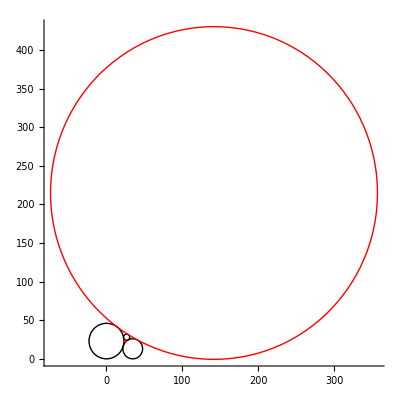

```mathematica
uDisplayFiveCircles[23,13,4]
```

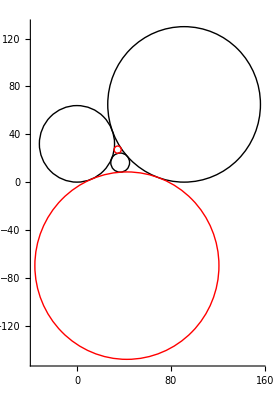

```mathematica
uDisplayFiveCircles[32,65,8]
```

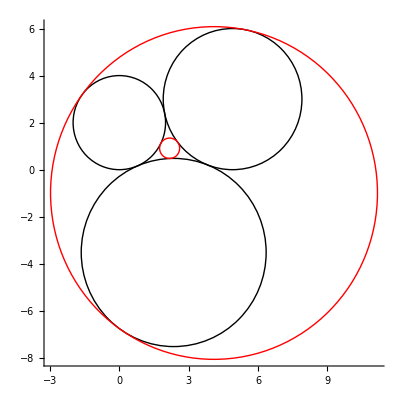

```mathematica
uDisplayFiveCircles[2,3,4]
```